# Математическое моделирование и сложные процессы.

## Лабораторная работа №6 Взаимодействие двух солитонов.

## Задача 1.

1) Получите в явном виде двусолитонное решение уравнения Кортевега- де Фриза. 
2) Проверьте, что полученный результат удовлетворяет уравнению.
3) Подберите параметры a_i и δ_i таким образом, чтобы обе волны двигались вправо, и более быстрая в нулевой момент времени находилась левее более медленной.
4) Рассчитайте и постройте анимированный график взаимодействия. Расстояние между волнами до начала и после окончания взаимодействия должно быть не менее, чем в 100 раз больше амплитуды большей волны.
5) Рассчитайте, насколько уменьшилась амплитуда большей волны (и увеличилась меньшей) во время взаимодействия.
6) Рассчитайте, к какому сдвигу фаз привело взаимдействие солитонов в сравнении с их уединенным движением.

### 1) Получите в явном виде двусолитонное решение уравнения Кортевега- де Фриза.

Будем искать решение уравнение КдФ в виде бегущей волны.

u_t+12 u u_x+u_(x x x)=0
Подставим функцию u = f(x-ct) в исходное уравнение. Проинтегрировав полученное уравнение, запишем уравнение нелинейного осциллятора: f''+6 f^2-c f-C=0
Это уравнение можно преобразовать к виду добавлением постоянной к неизвестной функции , при условии, что a^2=c^2+24 C≥0: 
f''+6 f^2-a^2 f=0

Умножим уравнение на f'  и проинтегрируем его:
 (f')^2+4 f^3-a^2 f^2=E. Данное уравнение описывает движение частицы в кубическом потенциале



При Е < 0 и f > 0частица совершает периодическое движение. Движение при E=0 соотвествует движению по сепаратрисе и решению в виде уединенной волны,
 Интегрируя (f')^2+4 f^3-a^2 f^2=0, получаем решение уравнения КдФ в виде уединенной бегущей волны:
u=1/4 a^2/(ch^2 1/2(a x-a^3 t+δ))


Уравнение можно преобразовать к виду u_t+∂/(∂ x)(6 u^2+u_xx)=0
Применим к этому уравнению подстановку Хопфа-Коула:
u=∂^2/(∂ x^2)ln f=∂/(∂ x)f_x/f=(f_xx f-f_x^2)/f^2=f_xx/f-(f_x/f)^2
Теперь можем свести его к однородному относительно функции f (нелинейному) уравнению Хироты
f f_(x t)-f_x f_t+3 f_xx^2+f f_(x x x x)-4 f_(x x x)f_x=0


Односолитонное решение для данного уравнения имеет вид f=1+ⅇ^θ, где θ=a x-a t^3+δ

Будем искать решение в виде разложения по некоторому малому параметру ϵ: 
f=1+∑_(i=1)^N ϵ^i f^(i)

Подставим  f=1+∑_(i=1)^N ϵ^i f^(i) в f f_(x t)-f_x f_t+3 f_xx^2+f f_(x x x x)-4 f_(x x x)f_x=0 и приравняв коэффициенты при разных степенях ϵ, получим систему уравнений:

(f^(1))_(x x x x)+(f^(1))_(x t)=0

(f^(2))_(x x x x)+(f^(2))_(x t)=-(f^(1)((f^(1))_(x x x x)+(f^(1))_(x t))-4(f^(1))_x(f^(1))_xxx+3((f^(1))_xx)^2-(f^(1))_x(f^(1))_t)

(f^(3))_(x x x x)+(f^(3))_(x t)=-(f^(1)((f^(2))_(x x x x)+(f^(2))_(x t))-4(f^(1))_x(f^(2))_xxx-4(f^(2))_x(f^(1))_xxx+6(f^(1))_xx(f^(2))_xx-(f^(1))_x(f^(2))_t-(f^(2))_x(f^(1))_t)

и т.д
Подставляя f^(1)в виде f^(1)=ⅇ^θ1+ⅇ^θ2, где θ=a x-a t^3+δ, для уравнения второго порядка получаем:
(f^(2))_(x x x x)+(f^(2))_xt=3 a_1 a_2(a_1-a_2)^2 ⅇ^(θ1+θ2)
Отсюда получаем f^(2)=((a_1-a_2)/(a_1+a_2))ⅇ^(θ1+θ2)

f_(x t)^(3)+f_(x x x x)^(3)=0
Важным свойством уравнения Хироты является тот факт,что при подстановке f^(1)и f^(2)в третье уравнение полученных коэффициентов его правая часть оказывается равной
нулю,что дает возможность оборвать разложение на третьем шаге

Пусть ϵ=1. Двухсолитонное решение КДФ получается по формулам
f=1+ⅇ^θ_1+ⅇ^θ_2+A ⅇ^(θ_1+θ_2), где θ_i=a_i x-a_i^3 t+δ_i, A=((a_1-a_2)/(a_1+a_2))^2
u=∂^2/(∂ x^2) ln f

```mathematica
f[x_,t_]:=1+∑_(i=1)^3 ϵ^i Subscript[f, i][x,t]
```

```mathematica
f[x,t]
```

1+ϵ f_1[x,t]+ϵ^2 f_2[x,t]+ϵ^3 f_3[x,t]

```mathematica
f Subscript[f, x t]-Subscript[f, x] Subscript[f, t]+3 Subscript[f, xx]^2+f Subscript[f, x x x x]-4 Subscript[f, x x x] Subscript[f, x]=0
```

Set::write: Tag Plus in -f_t\ f_x + f\ f_t\ x - 4\ f_x\ f_x^3 + f\ f_x^4 + 3\ f_xx 2 is Protected.

0

```mathematica
fun=f[x,t] D[f[x,t],x,t]-D[f[x,t],x]D[f[x,t],t]+3 D[f[x,t],x,x]^2+f[x,t] D[f[x,t],x,x,x,x]-4 D[f[x,t],x,x,x]D[f[x,t],x]
```

-(ϵ f_1^(0,1)[x,t]+ϵ^2 f_2^(0,1)[x,t]+ϵ^3 f_3^(0,1)[x,t]) (ϵ f_1^(1,0)[x,t]+ϵ^2 f_2^(1,0)[x,t]+ϵ^3 f_3^(1,0)[x,t])+(1+ϵ f_1[x,t]+ϵ^2 f_2[x,t]+ϵ^3 f_3[x,t]) (ϵ f_1^(1,1)[x,t]+ϵ^2 f_2^(1,1)[x,t]+ϵ^3 f_3^(1,1)[x,t])+3 (ϵ f_1^(2,0)[x,t]+ϵ^2 f_2^(2,0)[x,t]+ϵ^3 f_3^(2,0)[x,t])^2-4 (ϵ f_1^(1,0)[x,t]+ϵ^2 f_2^(1,0)[x,t]+ϵ^3 f_3^(1,0)[x,t]) (ϵ f_1^(3,0)[x,t]+ϵ^2 f_2^(3,0)[x,t]+ϵ^3 f_3^(3,0)[x,t])+(1+ϵ f_1[x,t]+ϵ^2 f_2[x,t]+ϵ^3 f_3[x,t]) (ϵ f_1^(4,0)[x,t]+ϵ^2 f_2^(4,0)[x,t]+ϵ^3 f_3^(4,0)[x,t])

```mathematica
Collect[fun,ϵ,Simplify]
```

ϵ (f_1^(1,1)[x,t]+f_1^(4,0)[x,t])+ϵ^2 (-f_1^(0,1)[x,t] f_1^(1,0)[x,t]+f_2^(1,1)[x,t]+3 (f_1^(2,0)[x,t])^2-4 f_1^(1,0)[x,t] f_1^(3,0)[x,t]+f_1[x,t] (f_1^(1,1)[x,t]+f_1^(4,0)[x,t])+f_2^(4,0)[x,t])+ϵ^3 (-f_2^(0,1)[x,t] f_1^(1,0)[x,t]-f_1^(0,1)[x,t] f_2^(1,0)[x,t]+f_2[x,t] f_1^(1,1)[x,t]+f_1[x,t] f_2^(1,1)[x,t]+f_3^(1,1)[x,t]+6 f_1^(2,0)[x,t] f_2^(2,0)[x,t]-4 f_2^(1,0)[x,t] f_1^(3,0)[x,t]-4 f_1^(1,0)[x,t] f_2^(3,0)[x,t]+f_2[x,t] f_1^(4,0)[x,t]+f_1[x,t] f_2^(4,0)[x,t]+f_3^(4,0)[x,t])+ϵ^4 (-f_3^(0,1)[x,t] f_1^(1,0)[x,t]-f_2^(0,1)[x,t] f_2^(1,0)[x,t]-f_1^(0,1)[x,t] f_3^(1,0)[x,t]+f_3[x,t] f_1^(1,1)[x,t]+f_2[x,t] f_2^(1,1)[x,t]+f_1[x,t] f_3^(1,1)[x,t]+3 (f_2^(2,0)[x,t])^2+6 f_1^(2,0)[x,t] f_3^(2,0)[x,t]-4 f_3^(1,0)[x,t] f_1^(3,0)[x,t]-4 f_2^(1,0)[x,t] f_2^(3,0)[x,t]-4 f_1^(1,0)[x,t] f_3^(3,0)[x,t]+f_3[x,t] f_1^(4,0)[x,t]+f_2[x,t] f_2^(4,0)[x,t]+f_1[x,t] f_3^(4,0)[x,t])+ϵ^5 (-f_3^(0,1)[x,t] f_2^(1,0)[x,t]-f_2^(0,1)[x,t] f_3^(1,0)[x,t]+f_3[x,t] f_2^(1,1)[x,t]+f_2[x,t] f_3^(1,1)[x,t]+6 f_2^(2,0)[x,t] f_3^(2,0)[x,t]-4 f_3^(1,0)[x,t] f_2^(3,0)[x,t]-4 f_2^(1,0)[x,t] f_3^(3,0)[x,t]+f_3[x,t] f_2^(4,0)[x,t]+f_2[x,t] f_3^(4,0)[x,t])+ϵ^6 (-f_3^(0,1)[x,t] f_3^(1,0)[x,t]+3 (f_3^(2,0)[x,t])^2-4 f_3^(1,0)[x,t] f_3^(3,0)[x,t]+f_3[x,t] (f_3^(1,1)[x,t]+f_3^(4,0)[x,t]))

```mathematica
coeff=CoefficientList[fun,ϵ]
```

{0,f_1^(1,1)[x,t]+f_1^(4,0)[x,t],-f_1^(0,1)[x,t] f_1^(1,0)[x,t]+f_1[x,t] f_1^(1,1)[x,t]+f_2^(1,1)[x,t]+3 (f_1^(2,0)[x,t])^2-4 f_1^(1,0)[x,t] f_1^(3,0)[x,t]+f_1[x,t] f_1^(4,0)[x,t]+f_2^(4,0)[x,t],-f_2^(0,1)[x,t] f_1^(1,0)[x,t]-f_1^(0,1)[x,t] f_2^(1,0)[x,t]+f_2[x,t] f_1^(1,1)[x,t]+f_1[x,t] f_2^(1,1)[x,t]+f_3^(1,1)[x,t]+6 f_1^(2,0)[x,t] f_2^(2,0)[x,t]-4 f_2^(1,0)[x,t] f_1^(3,0)[x,t]-4 f_1^(1,0)[x,t] f_2^(3,0)[x,t]+f_2[x,t] f_1^(4,0)[x,t]+f_1[x,t] f_2^(4,0)[x,t]+f_3^(4,0)[x,t],-f_3^(0,1)[x,t] f_1^(1,0)[x,t]-f_2^(0,1)[x,t] f_2^(1,0)[x,t]-f_1^(0,1)[x,t] f_3^(1,0)[x,t]+f_3[x,t] f_1^(1,1)[x,t]+f_2[x,t] f_2^(1,1)[x,t]+f_1[x,t] f_3^(1,1)[x,t]+3 (f_2^(2,0)[x,t])^2+6 f_1^(2,0)[x,t] f_3^(2,0)[x,t]-4 f_3^(1,0)[x,t] f_1^(3,0)[x,t]-4 f_2^(1,0)[x,t] f_2^(3,0)[x,t]-4 f_1^(1,0)[x,t] f_3^(3,0)[x,t]+f_3[x,t] f_1^(4,0)[x,t]+f_2[x,t] f_2^(4,0)[x,t]+f_1[x,t] f_3^(4,0)[x,t],-f_3^(0,1)[x,t] f_2^(1,0)[x,t]-f_2^(0,1)[x,t] f_3^(1,0)[x,t]+f_3[x,t] f_2^(1,1)[x,t]+f_2[x,t] f_3^(1,1)[x,t]+6 f_2^(2,0)[x,t] f_3^(2,0)[x,t]-4 f_3^(1,0)[x,t] f_2^(3,0)[x,t]-4 f_2^(1,0)[x,t] f_3^(3,0)[x,t]+f_3[x,t] f_2^(4,0)[x,t]+f_2[x,t] f_3^(4,0)[x,t],-f_3^(0,1)[x,t] f_3^(1,0)[x,t]+f_3[x,t] f_3^(1,1)[x,t]+3 (f_3^(2,0)[x,t])^2-4 f_3^(1,0)[x,t] f_3^(3,0)[x,t]+f_3[x,t] f_3^(4,0)[x,t]}

```mathematica
ee1=coeff⟦2⟧
```

f_1^(1,1)[x,t]+f_1^(4,0)[x,t]

```mathematica
ee1==0
```

f_1^(1,1)[x,t]+f_1^(4,0)[x,t]==0

```mathematica
ee2=coeff⟦3⟧//Simplify
```

-f_1^(0,1)[x,t] f_1^(1,0)[x,t]+f_2^(1,1)[x,t]+3 (f_1^(2,0)[x,t])^2-4 f_1^(1,0)[x,t] f_1^(3,0)[x,t]+f_1[x,t] (f_1^(1,1)[x,t]+f_1^(4,0)[x,t])+f_2^(4,0)[x,t]

```mathematica
ee2==0
```

-f_1^(0,1)[x,t] f_1^(1,0)[x,t]+f_2^(1,1)[x,t]+3 (f_1^(2,0)[x,t])^2-4 f_1^(1,0)[x,t] f_1^(3,0)[x,t]+f_1[x,t] (f_1^(1,1)[x,t]+f_1^(4,0)[x,t])+f_2^(4,0)[x,t]==0

```mathematica
ee3=coeff⟦4⟧//Simplify
```

-f_2^(0,1)[x,t] f_1^(1,0)[x,t]-f_1^(0,1)[x,t] f_2^(1,0)[x,t]+f_2[x,t] f_1^(1,1)[x,t]+f_1[x,t] f_2^(1,1)[x,t]+f_3^(1,1)[x,t]+6 f_1^(2,0)[x,t] f_2^(2,0)[x,t]-4 f_2^(1,0)[x,t] f_1^(3,0)[x,t]-4 f_1^(1,0)[x,t] f_2^(3,0)[x,t]+f_2[x,t] f_1^(4,0)[x,t]+f_1[x,t] f_2^(4,0)[x,t]+f_3^(4,0)[x,t]

```mathematica
ee3==0
```

-f_2^(0,1)[x,t] f_1^(1,0)[x,t]-f_1^(0,1)[x,t] f_2^(1,0)[x,t]+f_2[x,t] f_1^(1,1)[x,t]+f_1[x,t] f_2^(1,1)[x,t]+f_3^(1,1)[x,t]+6 f_1^(2,0)[x,t] f_2^(2,0)[x,t]-4 f_2^(1,0)[x,t] f_1^(3,0)[x,t]-4 f_1^(1,0)[x,t] f_2^(3,0)[x,t]+f_2[x,t] f_1^(4,0)[x,t]+f_1[x,t] f_2^(4,0)[x,t]+f_3^(4,0)[x,t]==0

### 2) Проверьте, что полученный результат удовлетворяет уравнению.

```mathematica
θ[a_,δ_,x_,t_]:=a x-a^3 t+δ
```

```mathematica
u[x_,t_,a1_,δ1_,a2_,δ2_]:=D[Log[1+ ⅇ^θ[a1,δ1,xx,t]+ⅇ^θ[a2,δ2,xx,t]+ ((a1-a2)/(a1+a2))^2 ⅇ^(θ[a1,δ1,xx,t]+θ[a2,δ2,xx,t])],{xx,2}]/.xx-> x
```

```mathematica
D[u[x,t,a1,a2,δ1,δ2],t]+12 u[x,t,a1,a2,δ1,δ2] D[u[x,t,a1,a2,δ1,δ2],x]+D[u[x,t,a1,a2,δ1,δ2],{x,3}]//FullSimplify
```

0

### 3) Подберите параметры a_i и δ_i таким образом, чтобы обе волны двигались вправо, и более быстрая в нулевой момент времени находилась левее более медленной.

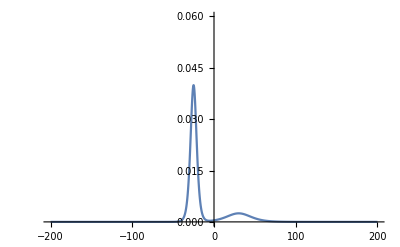

```mathematica
Plot[u[x,0,.4,10,.1,-2],{x,-200,200},PlotRange->{{-200,200},{0,0.06}}]
```

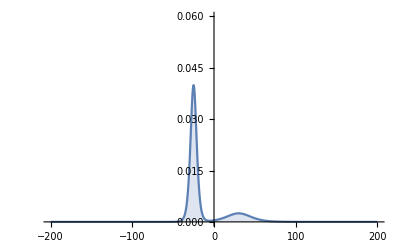
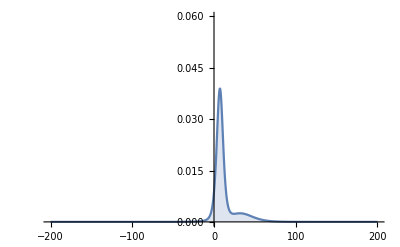
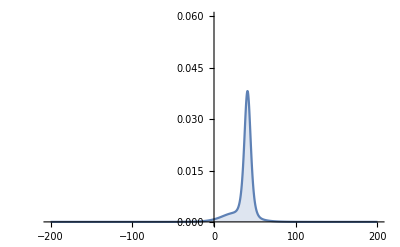
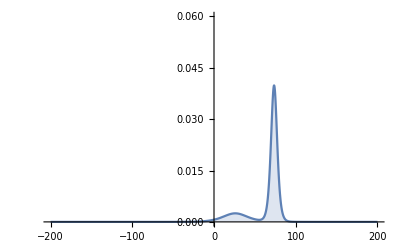
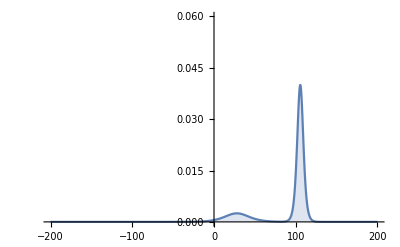
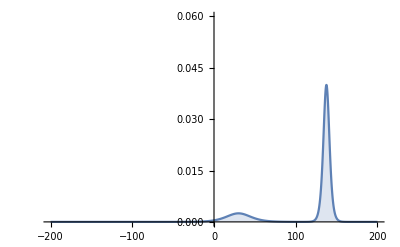

```mathematica
Table[Plot[u[x1,t,.4,10,.1,-2],{x1,-200,200},PlotRange->{{-200,200},{0,0.06}},Filling->Axis],{t,0,1000,200}]
```

```mathematica
Manipulate[
Plot[u[x,t,a1,δ1,a2,δ2],{x,-200,200},PlotRange->{{-200,200},{0,0.1}}]
,{t,0,1000},{{a1,.4},-1,10},{{δ1,30},-30,30},{{a2,.1},-1,10},{{δ2,1},-30,30}]
```

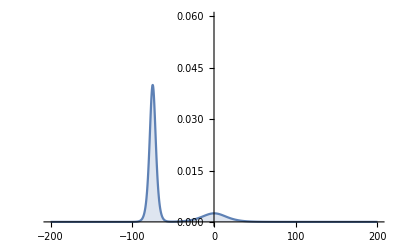
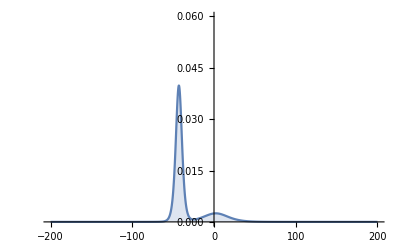
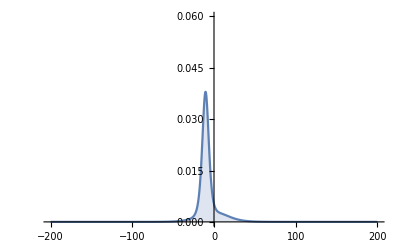
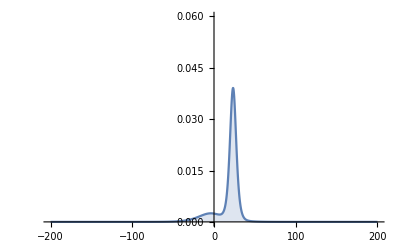
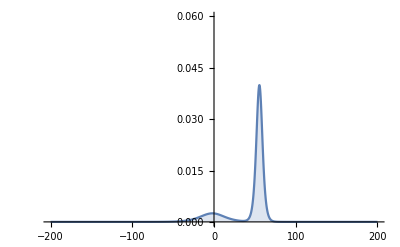
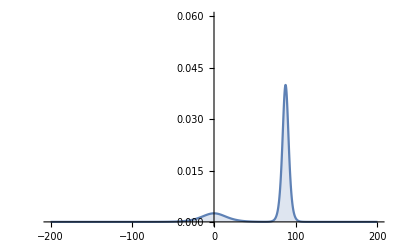

```mathematica
Table[Plot[u[x1,t,.4,30,.1,1],{x1,-200,200},PlotRange->{{-200,200},{0,0.06}},Filling->Axis],{t,0,1000,200}]
```

```mathematica
Manipulate[
Plot[u[x,t,a1,δ1,a2,δ2],{x,-200,200},PlotRange->{{-200,200},{0,0.1}}]
,{t,0,1000},{{a1,.4},-1,10},{{δ1,15},-30,30},{{a2,.2},-1,10},{{δ2,1},-30,30}]
```

### 4) Рассчитайте и постройте анимированный график взаимодействия. Расстояние между волнами до начала и после окончания взаимодействия должно быть не менее, чем в 100 раз больше амплитуды большей волны.

{a1,.4},-1,10},{{δ1,30},-30,30},{{a2,.1},-1,10},{{δ2,1},-30,30}]

```mathematica
ClearAll[a,x,t,θ,u,δ,a1,a2,δ1,δ2,x1,x2]
```

```mathematica
θ[t_,x_,a_,δ_]=a x-a^3 t+δ;
```

```mathematica
u[t_,x_,a1_,a2_,δ1_,δ2_]=D[Log[1+ (ⅇ^θ[t,x,a1,δ1]+ⅇ^θ[t,x,a2,δ2])+((a1-a2)/(a1+a2))^2 ⅇ^(θ[t,x,a1,δ1]+θ[t,x,a2,δ2])],{x,2}];
```

```mathematica
u1=u[t,x,a1,0,δ1,0]//Simplify
u2=u[t,x,0,a2,0,δ2]//Simplify
```

(a1^2 ⅇ^(a1^3 t+a1 x+δ1))/((ⅇ^(a1^3 t)+ⅇ^(a1 x+δ1))^2)

(a2^2 ⅇ^(a2^3 t+a2 x+δ2))/((ⅇ^(a2^3 t)+ⅇ^(a2 x+δ2))^2)

```mathematica
Off[Solve::ifun]
```

```mathematica
x1=Solve[D[u1,x]==0,x]⟦1,1,2⟧/.{t->0}
x2=Solve[D[u2,x]==0,x]⟦1,1,2⟧/.{t->0}
```

(-2 δ1+Log[ⅇ^δ1])/a1

(-2 δ2+Log[ⅇ^δ2])/a2

Амплитуды

```mathematica
A1=u1/.{x->x1,t->0}
A2=u2/.{x->x2,t->0}
```

a1^2/4

a2^2/4

```mathematica
ClearAll[x1,x2,a1,a2,δ1,δ2,T]
```

```mathematica
x1=Solve[D[u1,x]==0,x]⟦1,1,2⟧
x2=Solve[D[u2,x]==0,x]⟦1,1,2⟧
```

(-a1^3 t-2 δ1+Log[ⅇ^(2 a1^3 t+δ1)])/a1

(-a2^3 t-2 δ2+Log[ⅇ^(2 a2^3 t+δ2)])/a2

условия задачи для нахождения неизвестных параметров

```mathematica
r1=(x2-x1)/A1/.{t->0}
r2=(x2-x1)/A1/.{t->T}
```

(4 (-(-2 δ1+Log[ⅇ^δ1])/a1+(-2 δ2+Log[ⅇ^δ2])/a2))/a1^2

(4 (-(-a1^3 T-2 δ1+Log[ⅇ^(2 a1^3 T+δ1)])/a1+(-a2^3 T-2 δ2+Log[ⅇ^(2 a2^3 T+δ2)])/a2))/a1^2

```mathematica
a1=.4;
δ1=30;
δ2=1;
```

```mathematica
{A1,A2}
```

{0.04,a2^2/4}

```mathematica
Off[Solve::ratnz]
```

```mathematica
a2=a2/.Solve[r1==100,{a2}]⟦1⟧//N
```

0.0140845

```mathematica
Clear[T]
```

```mathematica
T/.Solve[r2==-100,{T}][[1]]
```

50.0621

```mathematica
T=T/.Solve[r2==-100,{T}][[1]]
```

50.0621

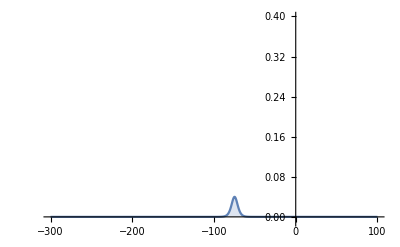

```mathematica
Plot[{u[0,x,a1,a2,δ1,δ2]},{x,-300,100},PlotRange->{{-300,100},{-0.01,.4}},Filling->Axis]
```

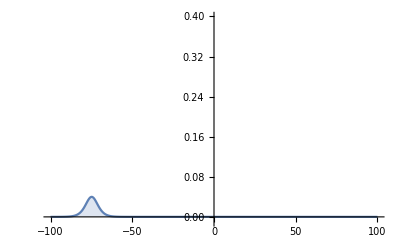

```mathematica
Plot[{Chop[u[0,x,a1,a2,δ1,δ2]]},{x,-100,100},PlotRange->{{-100,100},{-0.01,.4}},Filling->Axis]
```

```mathematica
Table[Plot[Chop[u[t,x,a1,a2,δ1,δ2]],{x,0,300},Filling->Axis,PlotRange->{{0,300},{-0.01, 1.2}}],{t,0,108,0.2}]//ListAnimate
```

## 5. Рассчитайте, насколько уменьшилась амплитуда большей волны (и увеличилась меньшей) во время взаимодействия

```mathematica
ClearAll[t,x]
tD=t/.Solve[x1==x2,t]⟦1⟧
xD=x1/.{t->tD}
```

52.331

136.165

```mathematica
A=u[tD,xD,{k1,k2},{χ1,χ2},ϵ]//Simplify
```

1.04867

```mathematica
A1/A//N
A2/A//N
```

1.07278

0.0477848

## 6. Рассчитайте, к какому сдвигу фаз привело взаимдействие солитонов в сравнении с их уединенным движением

```mathematica
1/k2 Log[Abs[(k2+k1)/(k2-k1)]]
```

1.35368

```mathematica
-1/k1 Log[Abs[(k2+k1)/(k2-k1)]]
```

-0.285696